## 所有一维数列都是向量

```mathematica
VectorQ[{1,2,3}]
```

True

```mathematica
MatrixForm[{{1,2},{2,5}}]
```

(1 | 2
2 | 5)

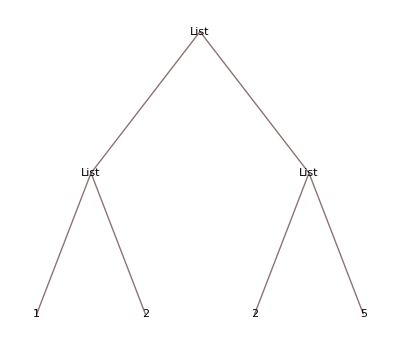

```mathematica
TreeForm[{{1,2},{2,5}}]
```

```mathematica
LeafCount[{{1,2},{2,5}}]
```

7

```mathematica
Head[2.2]
```

Real

```mathematica
Head[2]
```

Integer

```mathematica
Head[2/5]
```

Rational

```mathematica
Head[I]
```

Complex

```mathematica
Head[Sqrt[-9]]
```

Complex

```mathematica
Sqrt[-3]
```

ⅈ √3

```mathematica
Head[Sqrt[-3]]
```

Times

```mathematica
{1,2,3,a,b,{10},15.5}/.x:{_?(Head[#]==Integer&)}:>x^5
```

{1,2,3,a,b,{100000},15.5}

```mathematica
{1,2,3,a,b,{10},15.5}/.x_?(Head[#]==Integer&):>x^5
```

{1,32,243,a,b,{100000},15.5}

```mathematica
{1,2,3,a,b,{10},15.5}/.{x_Integer}:>x^5
```

{1,2,3,a,b,100000,15.5}

```mathematica
{1,2,3,a,b,{10},15.5}/.x_Integer:>x^5
```

{1,32,243,a,b,{100000},15.5}

```mathematica
{2,3,7/8,a}/.(x_?NumberQ)->x^2
```

{4,9,49/64,a}

```mathematica
{2,3,7/8,a}/.(x_Symbol)->x^2
```

List^2[2,3,7/8,a^2]

## 条件函数

```mathematica
f[x_?Positive]:=Sqrt[x]
```

```mathematica
f[-1]
```

f[-1]

```mathematica
f[4]
```

2

```mathematica
Clear[f]
f[x_]:=x^2/;ListQ[x]
```

```mathematica
Clear[f]
f[x_]/;ListQ[x]:=x^2
```

```mathematica
Clear[f]
f[x_/;ListQ[x]]:=x^2
```

```mathematica
f[2]
```

f[2]

```mathematica
f[{2}]
```

{4}

## 纯函数、条件与替换结合

```mathematica
#/.x_/;x>5:>x^5&[{1,2,3,10}]
```

{1,2,3,100000}

```mathematica
{1,2,3,10,15.5}/.x_List:>x^2
```

{1,4,9,100,240.25}

```mathematica
{1,2,3,10,15.5}/.x_Integer:>x^2
```

{1,4,9,100,15.5}

```mathematica
#/.x_Integer:>x^2&[{1,2,3,10,15.5}]
```

{1,4,9,100,15.5}

```mathematica
#/.x_/;NumberQ[x]:>x^2&[{1,2,3,1,a,b,15.5}]
```

{1,4,9,1,a,b,240.25}

```mathematica
#/.x_?(NumberQ[#]&):>x^2&[{1,2,3,1,a,b,15.5}]
```

{1,4,9,1,a,b,240.25}

```mathematica
|表示一种或者or的逻辑，只要有一个满足就可以
And表示并且的意思，必须全部同时满足才算通过
```

```mathematica
{1,2,3,10,a,15.5,True}/.x_Integer|x_Real:>x^2
```

{1,4,9,100,a,240.25,True}

```mathematica
{1,2,3,10,a,15.5,True}/.x_Integer |x_Real|x_?BooleanQ:>x^2
```

{1,4,9,100,a,240.25,True^2}

```mathematica
{1,2,3,10,a,15.5,True}/.{x_Integer |x_Real:>x^2 , x_?BooleanQ:>x^3}
```

{1,4,9,100,a,240.25,True^3}

```mathematica
满足多个要求
```

```mathematica
#/.x_Integer?(OddQ[#]&):>x^2&[{1,2,3,10,a,15.5,13}]
```

{1,2,9,10,a,15.5,169}

```mathematica
#/.x_Integer?(#>5&):>x^2&[{1,2,3,10,a,15.5,13}]
```

{1,2,3,100,a,15.5,169}

```mathematica
#/.x_Integer?(#>5∧OddQ[#]∧PrimeQ[#]&):>x^2&[{1,2,3,10,a,15.5,13,15}]
```

{1,2,3,10,a,15.5,169,15}

### 运算有顺序

```mathematica
{1,2,3,10,a,15.5,True}/.{x_Integer:>x ,x_Real:>x^2 , x_?BooleanQ:>x^3}
```

{1,2,3,10,a,240.25,True^3}

```mathematica
{1,2,3,10,a,15.5,True}/.{x_Real:>x ,x_Integer:>x^2 , x_?BooleanQ:>x^3}
```

{1,4,9,100,a,15.5,True^3}

```mathematica
加入逻辑符号
```

```mathematica
{1,2,3,10,a,15.5,3I,True}/.x_?IntegerQ|x_Real|_Complex|x_?(#∈Booleans&):>(x*100)
```

{100,200,300,1000,a,1550.,100,100 True}

```mathematica
{1,2,3,10,a,15.5,3I,True}/.x_?IntegerQ|x_Real|x_Complex|x_?(#∈Booleans&):>(x*100)
```

{100,200,300,1000,a,1550.,300 ⅈ,100 True}

```mathematica
{2,3.5,3I}/.x_Integer:>x*100
```

{200,3.5,3 ⅈ}

```mathematica
{2,3.5,3I}/._Integer:>x*100
```

{100 x,3.5,3 ⅈ}

## Test if an expression cannot be subdivided:

```mathematica
AtomQ[2]
```

True

```mathematica
AtomQ[1.2]
```

True

```mathematica
AtomQ[2/3]
```

True

```mathematica
AtomQ[2/4]
```

True

```mathematica
MemberQ[{1,2,3},{1}]
```

False

```mathematica
MemberQ[{1,2,3},1]
```

True

```mathematica
NumberQ[{1,2,3}]
```

False

```mathematica
ListQ[{1,2,3}]
```

True

## 符号输入：Basic Math Assistant, Writing Assistant 集合运算 ℕ⊂ℤ⊂ℝ⊂ℂ 逻辑发展： Syllogism ->Logics-> Symbol Logics ->logic gates (And, OR, XOR

```mathematica
({{1, 2}, {4, 6}})
({{1, □, □, 5, □}, {□, □, □, □, □}, {□, □, 3, □, □}, {□, □, □, 3, □}, {□, □, □, □, □}})
```

## 矩阵运算

```mathematica
{a,b}*{2,3}
```

{2 a,3 b}

```mathematica
{{a,b},{c,d}}*{x,y}
```

{{a x,b x},{c y,d y}}

```mathematica
{{a,b},{c,d}}.{x,y}
```

{a x+b y,c x+d y}

```mathematica
{a,b}^2
```

{a^2,b^2}

```mathematica
{a,b}+{1,2,3}
```

Thread::tdlen: Objects of unequal length in {a,b}+{1,2,3} cannot be combined.

{a,b}+{1,2,3}

```mathematica
{a,b,c}*{x,y,z}
```

{a x,b y,c z}

```mathematica
{a,b,c}.{x,y,z}
```

a x+b y+c z

```mathematica
{{a,b},{c,d}}*{x,y}
```

{{a x,b x},{c y,d y}}

```mathematica
{{a,b},{c,d}}.{x,y}
```

{a x+b y,c x+d y}

```mathematica
{{a,b},{c,d}}*{{1,2},{3,4}}
```

{{a,2 b},{3 c,4 d}}

```mathematica
{{a,b},{c,d}}.{{1,2},{3,4}}
```

{{a+3 b,2 a+4 b},{c+3 d,2 c+4 d}}

```mathematica
.会消解一层结构，而*不会
```

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
N[Sqrt[2],10]
```

1.414213562

```mathematica
Sqrt[2]
```

√2

```mathematica
Pi
```

π

```mathematica
j=1;
Table[j++,10]
```

{1,2,3,4,5,6,7,8,9,10}